```mathematica
SetDirectory[NotebookDirectory[]];
```

## Presné riešenie

{{19.4356,-14.2279}}

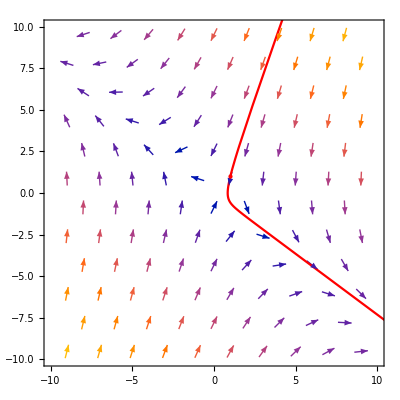

```mathematica
ExactSolution[x0_,y0_,t0_,t1_, plotRangeX_, plotRangeY_] := Module[{x, y, M, exactSolution},{
M={{0,-1/2}, {-1,-1}};
exactSolution = DSolve[{
{x'[t],y'[t]}==M.{x[t],y[t]},
x[0]==x0, y[0]==y0},{x,y}, t ];
Print[{x[t], y[t]}/.exactSolution/.t->t1//N];
{
VectorPlot[M.{x,y},Flatten[{x,plotRangeX}], Flatten[{y,plotRangeY}],VectorPoints->Coarse, VectorSizes->0.5],
ParametricPlot[{{x[t], y[t]}/.exactSolution}, {t,t0,t1}, PlotStyle->Red],
Graphics[{Red,PointSize[Large],Point[{x0,y0}]}]
}
}]
Show[ExactSolution[1,1,-10,10, {-10,10}, {-10,10}]]
```

## Explicitná Eulerova metóda

### {5, 5}

{{7.53749,-5.37403}}

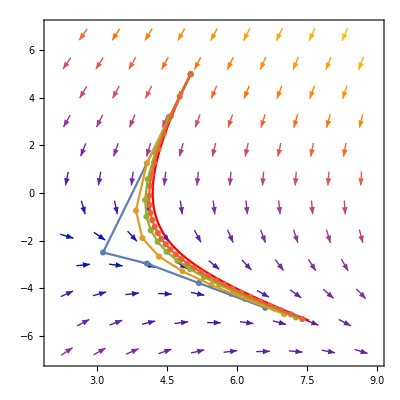

```mathematica
numerics = {Import["./outputs/EEM_5_5_4n.csv","CSV"],
Import["./outputs/EEM_5_5_8n.csv","CSV"],
Import["./outputs/EEM_5_5_16n.csv","CSV"],
Import["./outputs/EEM_5_5_32n.csv","CSV"]};
Show[
ExactSolution[5,5,0,3, {2,9}, {-7,7}],
ListPlot[numerics],
ListLinePlot[numerics]
]
```

### {-2, -7}

{{8.28843,-6.0677}}

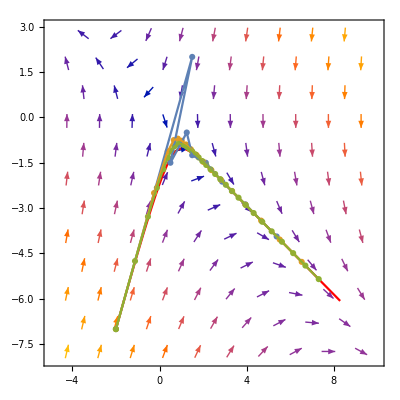

```mathematica
numerics = {Import["./outputs/EEM_-2_-7_8n.csv","CSV"],
Import["./outputs/EEM_-2_-7_16n.csv","CSV"],
Import["./outputs/EEM_-2_-7_32n.csv","CSV"]};
Show[
ExactSolution[-2,-7,0,8,{-5,10}, {-8,3}],
ListPlot[numerics],
ListLinePlot[numerics]
]
```

### {-3, -7}

{{-9.30812,6.81397}}

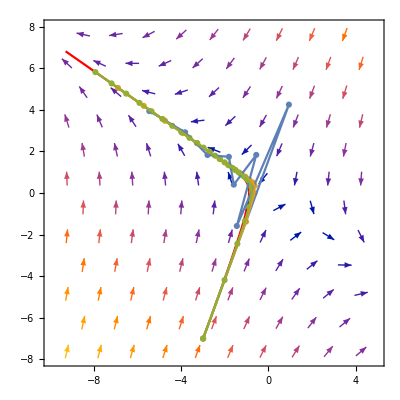

```mathematica
numerics = {Import["./outputs/EEM_-3_-7_8n.csv","CSV"],
Import["./outputs/EEM_-3_-7_16n.csv","CSV"],
Import["./outputs/EEM_-3_-7_32n.csv","CSV"]};
Show[
ExactSolution[-3,-7,0,9,{-10,5}, {-8,8}],
ListPlot[numerics],
ListLinePlot[numerics]
]
```

## RK2 metóda

### {5, 5}

{{7.53749,-5.37403}}

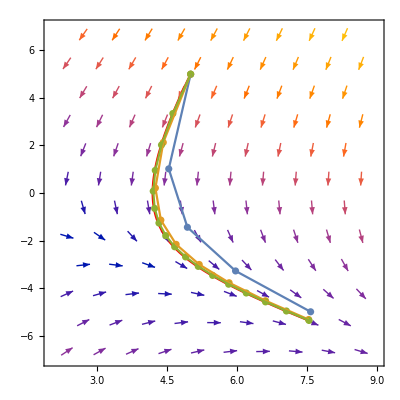

```mathematica
numerics = {Import["./outputs/RK2_5_5_4n.csv","CSV"],
Import["./outputs/RK2_5_5_8n.csv","CSV"],
Import["./outputs/RK2_5_5_16n.csv","CSV"]};
Show[
ExactSolution[5,5,0,3, {2,9}, {-7,7}],
ListPlot[numerics],
ListLinePlot[numerics]
]
```

### {-2, -7}

{{8.28843,-6.0677}}

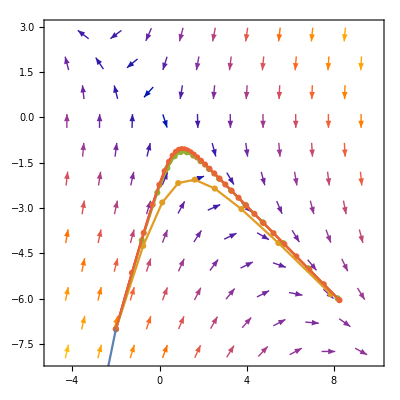

```mathematica
numerics = {Import["./outputs/RK2_-2_-7_4n.csv","CSV"],
Import["./outputs/RK2_-2_-7_8n.csv","CSV"],
Import["./outputs/RK2_-2_-7_16n.csv","CSV"],
Import["./outputs/RK2_-2_-7_32n.csv","CSV"]};
Show[
ExactSolution[-2,-7,0,8,{-5,10}, {-8,3}],
ListPlot[numerics],
ListLinePlot[numerics]
]
```

### {-3, -7}

{{-9.30812,6.81397}}

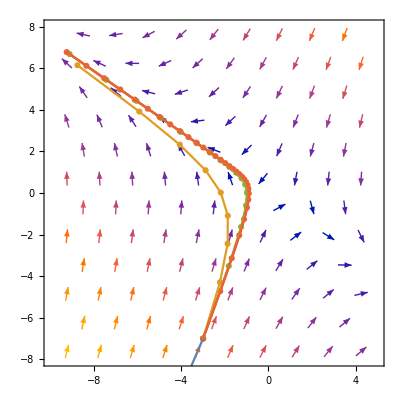

```mathematica
numerics = {Import["./outputs/RK2_-3_-7_8n.csv","CSV"],
Import["./outputs/RK2_-3_-7_16n.csv","CSV"],
Import["./outputs/RK2_-3_-7_32n.csv","CSV"]};
Show[
ExactSolution[-3,-7,0,9,{-10,5}, {-8,8}],
ListPlot[numerics],
ListLinePlot[numerics]
]
```

## RK4 metóda

### {5, 5}

{{7.53749,-5.37403}}

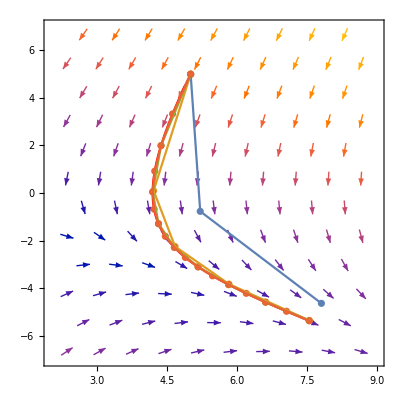

```mathematica
numerics = {Import["./outputs/RK4_5_5_2n.csv","CSV"],
Import["./outputs/RK4_5_5_4n.csv","CSV"],
Import["./outputs/RK4_5_5_8n.csv","CSV"],
Import["./outputs/RK4_5_5_16n.csv","CSV"]};
Show[
ExactSolution[5,5,0,3, {2,9}, {-7,7}],
ListPlot[numerics],
ListLinePlot[numerics]
]
```

### {-2, -7}

{{8.28843,-6.0677}}

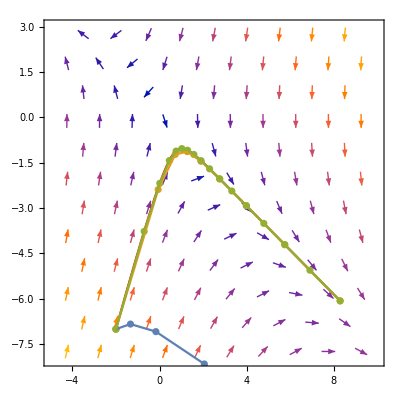

```mathematica
numerics = {Import["./outputs/RK4_-2_-7_4n.csv","CSV"],
Import["./outputs/RK4_-2_-7_8n.csv","CSV"],
Import["./outputs/RK4_-2_-7_16n.csv","CSV"]};
Show[
ExactSolution[-2,-7,0,8,{-5,10}, {-8,3}],
ListPlot[numerics],
ListLinePlot[numerics]
]
```

### {-3, -7}

{{-9.30812,6.81397}}

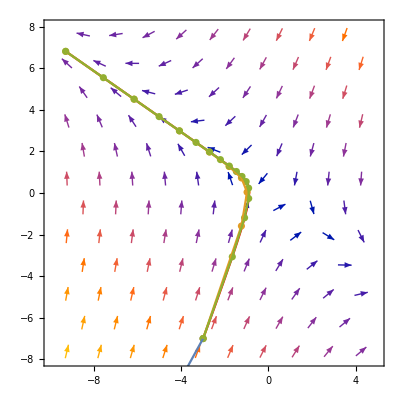

```mathematica
numerics = {Import["./outputs/RK4_-3_-7_4n.csv","CSV"],
Import["./outputs/RK4_-3_-7_8n.csv","CSV"],
Import["./outputs/RK4_-3_-7_16n.csv","CSV"]};
Show[
ExactSolution[-3,-7,0,9,{-10,5}, {-8,8}],
ListPlot[numerics],
ListLinePlot[numerics]
]
```

## 3-kroková Adams-Moulton metóda

### Výpočet

```mathematica
f[x_,y_]=-1/2 y;
g[x_,y_]=-x-y;
AM2Step = Solve[{
x1==x0+h/2(f[x0,y0]+f[x1,y1]),
y1==y0+h/2(g[x0,y0]+g[x1,y1])
},{x1,y1}]
AM2Step = Solve[{
x2==x1+h/12(-f[x0,y0]+8f[x1,y1]+5f[x2,y2]),
y2==y1+h/12(-g[x0,y0]+8g[x1,y1]+5g[x2,y2])
},{x2,y2}]
AM3Step=Solve[{
x3==x2+h/24(f[x0,y0]-5f[x1,y1]+19f[x2,y2]+9f[x3,y3]),
y3==y2+h/24(g[x0,y0]-5g[x1,y1]+19g[x2,y2]+9g[x3,y3])
},{x3,y3}]
```

{{x1→-(8 x0+4 h x0+h^2 x0-4 h y0)/(-8-4 h+h^2),y1→-((-8 h x0+8 y0-4 h y0+h^2 y0)/(-8-4 h+h^2))}}

{{x2→-((-5 h^2 x0+288 x1+120 h x1+40 h^2 x1+12 h y0-156 h y1)/(-288-120 h+25 h^2)),y2→-((24 h x0-312 h x1+24 h y0-5 h^2 y0+288 y1-192 h y1+40 h^2 y1)/(-288-120 h+25 h^2))}}

{{x3→-((3 h^2 x0-15 h^2 x1+384 x2+144 h x2+57 h^2 x2-8 h y0+40 h y1-224 h y2)/(3 (-128-48 h+9 h^2))),y3→-((-16 h x0+80 h x1-448 h x2-16 h y0+3 h^2 y0+80 h y1-15 h^2 y1+384 y2-304 h y2+57 h^2 y2)/(3 (-128-48 h+9 h^2)))}}

### {5, 5}

{{7.53749,-5.37403}}

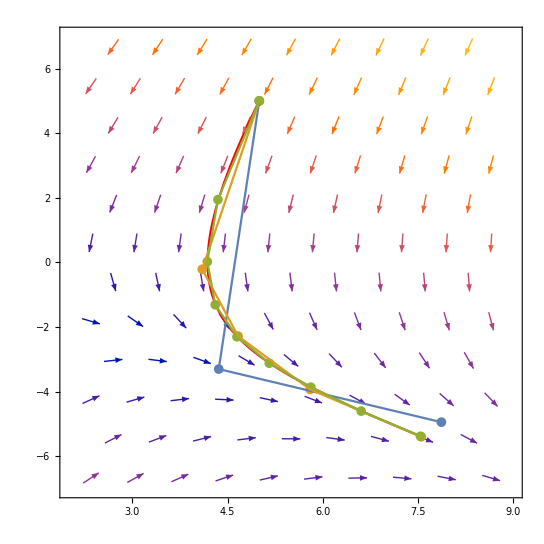

```mathematica
numerics = {Import["./outputs/AM3_5_5_2n.csv","CSV"],
Import["./outputs/AM3_5_5_4n.csv","CSV"],
Import["./outputs/AM3_5_5_8n.csv","CSV"](*
Import["./outputs/AM3_5_5_16n.csv","CSV"]*)};
Show[
ExactSolution[5,5,0,3, {2,9}, {-7,7}],
ListPlot[numerics],
ListLinePlot[numerics]
]
```

### {-2, -7}

```mathematica
numerics = {Import["./outputs/RK4_-2_-7_4n.csv","CSV"],
Import["./outputs/RK4_-2_-7_8n.csv","CSV"],
Import["./outputs/RK4_-2_-7_16n.csv","CSV"]};
Show[
ExactSolution[-2,-7,0,8,{-5,10}, {-8,3}],
ListPlot[numerics],
ListLinePlot[numerics]
]
```

{{8.28843,-6.0677}}

-Graphics-

### {-3, -7}

```mathematica
numerics = {Import["./outputs/RK4_-3_-7_4n.csv","CSV"],
Import["./outputs/RK4_-3_-7_8n.csv","CSV"],
Import["./outputs/RK4_-3_-7_16n.csv","CSV"]};
Show[
ExactSolution[-3,-7,0,9,{-10,5}, {-8,8}],
ListPlot[numerics],
ListLinePlot[numerics]
]
```

{{-9.30812,6.81397}}

-Graphics-